```mathematica
comp1[x_] := 1.0*x/(1.0*x*1.0*Exp[1.0*x]*1.0*Exp[1.0*Sin[1.0*x+1.0]]+1.0*Exp[1.0*x]*1.0*Exp[1.0*Sin[1.0*x+1.0]])+1.0
comp2[x_] := 1.0*Sqrt[1.0*Abs[1.0*Sqrt[1.0*Abs[1.0*x+1.0]]]]*1.0*Sin[1.0*x/(1.0*x+1.0)+1.0/(1.0*x+1.0)]+1.0
comp3[x_] := 1.0*Sqrt[1.0*Abs[1.0*x/(1.0*x+1.0)+1.0/(1.0*x+1.0)]]+1.0*Sqrt[1.0*Abs[1.0*Exp[1.0*x]]]+1.0
comp4[x_] := 1.0*Sqrt[1.0*Abs[1.0*x]]+1.0/(x*1.0*Sqrt[1.0*Abs[1.0*x]]*1.0*Sqrt[1.0*Abs[1.0*x]])+1.0
comp5[x_] := 1.0*x/(1.0*x*1.0*Sqrt[1.0*Abs[1.0*Log[1.0*x]]]+1.0*Sqrt[1.0*Abs[1.0*Log[1.0*x]]])+1.0
comp6[x_] := 1.0*x^2*1.0*Sqrt[1.0*Abs[1.0*x+1.0]]+1.0*x+1.0*x/(1.0*x)+1.0*Log[1.0*x+1.0]+1.0
comp7[x_] := 1.0*Sqrt[1.0*Abs[1.0*x*1.0*Sqrt[1.0*Abs[1.0*x]]/(1.0*x+1.0)+1.0/(1.0*x+1.0)]]+1.0
comp8[x_] := 1.0*x^2+1.0*x+1.0*Exp[1.0*x]/1.0*Sqrt[1.0*Abs[1.0*Sqrt[1.0*Abs[1.0*x+1.0]]]]+1.0
myEqns = {comp1, comp2, comp3, comp4, comp5, comp6, comp7, comp8};
```

```mathematica
Print["Complicated Benchmark Equations"]
Do[Print[Simplify[eqn[x]]," evaluated at 0.1 = ", N[eqn[.1]]];,
 {eqn, myEqns
}]
```

Complicated Benchmark Equations

1.+(1. ⅇ^(-1. x-1. Sin[1.+1. x]) x)/(1.+1. x) evaluated at 0.1 = 1.03374

1.+0.841471 Abs[1.+1. x]^(1/4) evaluated at 0.1 = 1.86176

2.+1. ⅇ^(0.5 Re[x]) evaluated at 0.1 = 3.05127

1.+1./(x Abs[x])+1. √Abs[x] evaluated at 0.1 = 101.316

1.+(1. x)/((1.+1. x) √Abs[0.+Log[x]]) evaluated at 0.1 = 1.05991

2.+1. x+1. x^2 √Abs[1.+1. x]+1. Log[1.+1. x] evaluated at 0.1 = 2.2058

1.+1. √Abs[(1.+1. x √Abs[x])/(1.+1. x)] evaluated at 0.1 = 1.96842

1.+1. x+1. x^2+1. ⅇ^(1. x) Abs[1.+1. x]^(1/4) evaluated at 0.1 = 2.24182

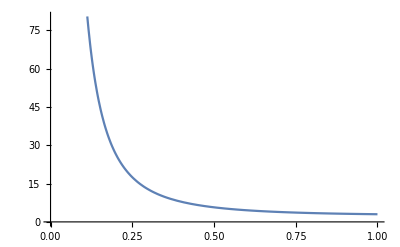

```mathematica
Plot[Part[myEqns,4][x], {x,0,1}]
```

```mathematica
rangeMin = {-3., -3., -3., 0.1, 1.01, -.9, -3., -3.};
rangeMax = {3., 3., 3., 4, 4, 3, 3., 3.};
numberSamples = 20;
numberTrials = 100;
timeLimit = 9;
```

```mathematica
For[
hh=1, hh<=8, hh++,
evals = {};
mses = {};
For[ii=1, ii<=numberTrials, ii++,
SeedRandom[ii];
myX = RandomReal[{Part[rangeMin,hh],Part[rangeMax,hh]},{numberSamples}];
y = Part[myEqns,hh][myX];

predFn = FindFormula[Transpose[{myX,y}],x,1, "Error", RandomSeeding->ii, TimeConstraint->timeLimit];
isCorrect =If[Simplify[Expand[Part[myEqns,hh][x]] ==Expand[Part[predFn,1]]],1,0,0];
myMSE = Part[predFn,2];

evals = Append[evals, isCorrect];
mses = Append[mses, myMSE];
];
Print["tgt eqn ", hh,": ", Simplify[Part[myEqns,hh][x]]];
Print["predicted: "Simplify[Part[predFn,1]]];
Print["Mean recovery = ", N[Mean[evals],4]];
Print["Mean MSE = ", N[Mean[mses],3]," +/- ", N[StandardDeviation[mses],3], " standard deviation"];
]
```

tgt eqn 1: 1.+(1. ⅇ^(-1. x-1. Sin[1.+1. x]) x)/(1.+1. x)

13.6029 predicted:

Mean recovery = 0

Mean MSE = 1180.98 +/- 2123.08 standard deviation

tgt eqn 2: 1.+0.841471 Abs[1.+1. x]^(1/4)

1.90018 predicted:

Mean recovery = 0

Mean MSE = 0.0399382 +/- 0.0144759 standard deviation

tgt eqn 3: 2.+1. ⅇ^(0.5 Re[x])

predicted:  (3.+0.499999 x+0.125001 x^2+0.0208351 x^3+0.00260397 x^4+0.000259743 x^5+0.0000217234 x^6+1.65366×10^-6 x^7+9.83783×10^-8 x^8)

Mean recovery = 0

Mean MSE = 0.0000313354 +/- 0.000212823 standard deviation

tgt eqn 4: 1.+1./(x Abs[x])+1. √Abs[x]

predicted:  (1.+1/x^2.+1. √x)

Mean recovery = 0

Mean MSE = 0.0413246 +/- 0.126884 standard deviation

tgt eqn 5: 1.+(1. x)/((1.+1. x) √Abs[0.+Log[x]])

predicted:  (1.72806+2.03642/x^6.03171)

Mean recovery = 0

Mean MSE = 0.0244879 +/- 0.0935473 standard deviation

tgt eqn 6: 2.+1. x+1. x^2 √Abs[1.+1. x]+1. Log[1.+1. x]

predicted:  (2.04065+7.49385 x-5.40613 Sin[x])

Mean recovery = 0

Mean MSE = 0.0270483 +/- 0.0408112 standard deviation

tgt eqn 7: 1.+1. √Abs[(1.+1. x √Abs[x])/(1.+1. x)]

2.21276 predicted:

Mean recovery = 0

Mean MSE = 0.0207129 +/- 0.00487009 standard deviation

tgt eqn 8: 1.+1. x+1. x^2+1. ⅇ^(1. x) Abs[1.+1. x]^(1/4)

(2.8995+3.52662^x) predicted:

Mean recovery = 0

Mean MSE = 3.5084 +/- 4.37031 standard deviation